```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<Segment.wl
```

```mathematica
<<Ocr.wl
```

```mathematica
ocrChinese@imageScaled[-Graphics-,5]
```

长久以来, 机器视觉认知一直是人们研究的热点, 它是研究使用机器或计算

```mathematica
plot:=ArrayPlot[#,ColorRules->{0->Blue,1->White,2->Red,3->Green},Mesh->All]&(*全黑会画成全白，坑了。用蓝代替黑*)
```

```mathematica
i=Import@"data/simple01.bmp"
```

-Graphics-

```mathematica
(*zhLines=i//segment//(#//splitByGreen//turnBlack/@#&//mergeSplitBy//Image[#,"Bit",Magnification->1]&//ColorNegate)&/@#&;*)
```

```mathematica
(*宽高比*)
ratioWidthHight[mts_]:=mts//Dimensions/@#&//(#[[1]]/#[[2]]&)/@#&
```

```mathematica
zhLines=i//imageLines//Take[#,3]&;
```

```mathematica
zhLines//TableForm
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
zhLines//imageScaled[#,5]&/@#&//ocrChinese/@#&//TableForm
```

第四部分 预测试卷
预测试卷( 一一*)
一丹单项选择题(共70  1 分口 每题的备选项中,只有 1 个最

```mathematica
greenReds=zhLines//labelGreenRed/@#&;
```

```mathematica
greenRed=zhLines//First//labelGreenRed;
```

```mathematica
characters=greenRed//splitByGreenClean;
```

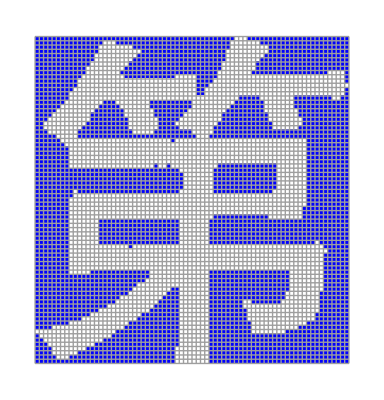
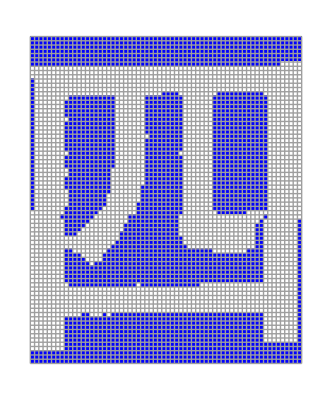
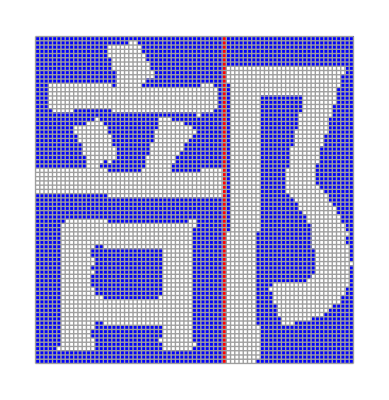
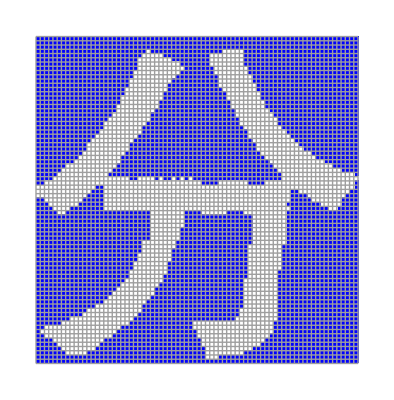
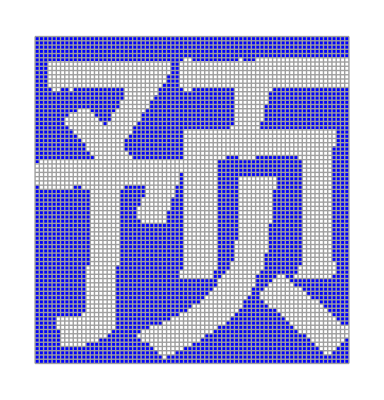
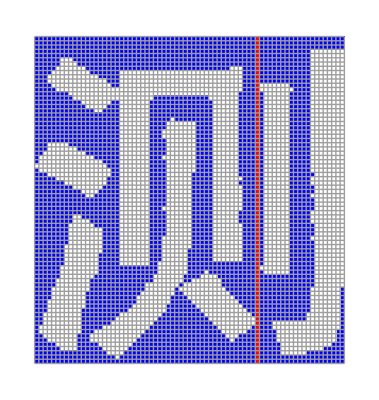
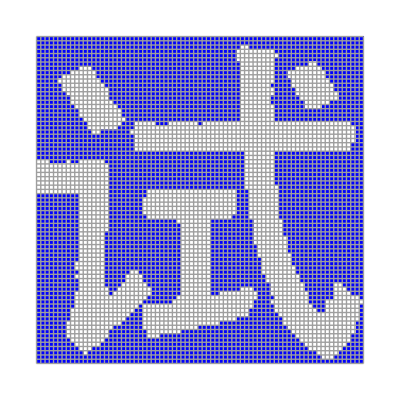
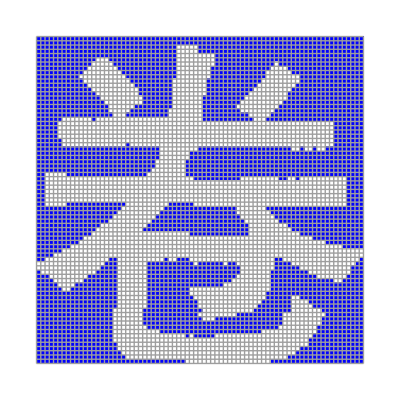

```mathematica
characters//plot/@#&
```

```mathematica
characterss=greenReds//splitByGreenClean/@#&;
```

```mathematica
characters=characterss//Flatten[#,1]&;
```

```mathematica
ratio=characters//ratioWidthHight//FindClusters//Sort[#, Length[#1]>Length[#2]&]&//First
```

{77/74,77/64,77/75,77/76,77/74,77/73,1,1,59/58,59/60,59/58,59/58,59/60,43/37,43/39,43/40,43/40,43/40,43/40,43/41,43/19,43/20,43/41,43/40,43/41,43/41,43/40,43/40,43/36,43/40,43/40,43/39,43/34,43/36,43/39,43/41,43/40,43/41,43/41,43/85}

```mathematica
characters//ratioWidthHight
```

{77/74,77/64,77/75,77/76,77/74,77/73,1,1,59/58,59/60,59/58,59/58,59/17,59/60,59/18,43/37,43/13,43/39,43/40,43/40,43/40,43/40,43/11,43/41,43/19,43/20,43/41,43/7,43/40,43/41,43/12,43/41,43/12,43/40,43/40,43/36,43/40,43/40,43/39,43/34,43/7,43/36,43/39,43/12,43/41,43/40,43/41,43/41,43/85,43/11}

```mathematica
(*Quit[]*)
```

```mathematica
characters//plot/@#&
```

```mathematica
label[width_,height_]:=StringTemplate["w `1`,h `2`"][width, height]
```

```mathematica
-Graphics-//Binarize//Show[#,Graphics[{Red,Text[#//ImageData//Dimensions//label@@#&,{Center,Center},Background->Blue]}]]&
```

```mathematica
characters//Image/@#&//Show[#,Graphics[{Red,Text[#//ImageData//Dimensions//label@@Reverse[#]&,{Center,Center},Background->Blue]}]]&/@#&
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}